### Start choosing the example:

```mathematica
t=6;
beta=0;
A=0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"]
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10},"Adjacency Matrix"->{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{10,U1}},"Switching Costs"->{}|>;
```

```mathematica
d2e=Data2Equations[Data/.{I1-> 80, U1-> 0}];
CriticalCongestionSolver[d2e]//AbsoluteTiming
```

j1==0&&j10==80&&j11==0&&j12==80&&j13==0&&j14==80&&j15==0&&j16==80&&j17==0&&j18==80&&j19==0&&j2==80&&j20==80&&j21==0&&j22==80&&j3==0&&j4==80&&j5==0&&j6==80&&j7==0&&j8==80&&j9==0&&jt1==0&&jt10==0&&jt11==80&&jt12==0&&jt13==80&&jt14==0&&jt15==80&&jt16==0&&jt17==80&&jt18==0&&jt19==80&&jt2==80&&jt20==0&&jt3==80&&jt4==0&&jt5==80&&jt6==0&&jt7==80&&jt8==0&&jt9==80&&u1==u21&&u10==u11&&-u10+u11==0&&u12==u13&&-u12+u13==0&&u14==u15&&-u14+u15==0&&u16==u17&&-u16+u17==0&&-u18==0&&u18==0&&u19==0&&u2==u3&&u20==0&&u1-u21==0&&u22==u21&&-u2+u3==0&&u4==u5&&-u4+u5==0&&u6==u7&&-u6+u7==0&&u8==u9&&-u8+u9==0

j1==0&&j10==80&&j11==0&&j12==80&&j13==0&&j14==80&&j15==0&&j16==80&&j17==0&&j18==80&&j19==0&&j2==80&&j20==80&&j21==0&&j22==80&&j3==0&&j4==80&&j5==0&&j6==80&&j7==0&&j8==80&&j9==0&&jt1==0&&jt10==0&&jt11==80&&jt12==0&&jt13==80&&jt14==0&&jt15==80&&jt16==0&&jt17==80&&jt18==0&&jt19==80&&jt2==80&&jt20==0&&jt3==80&&jt4==0&&jt5==80&&jt6==0&&jt7==80&&jt8==0&&jt9==80&&u11==u10&&u13==u12&&u15==u14&&u17==u16&&u18==0&&u19==0&&u20==0&&u21==u1&&u22==u1&&u3==u2&&u5==u4&&u7==u6&&u9==u8

Checking (replacing updated rules in both systems)...

Ok!

FinalClean...

NewReduce of Not[Or OR And]: True

{0.009017,<|j22→80,j21→0,j19→0,j2→80,j1→0,j4→80,j3→0,j6→80,j5→0,j8→80,j7→0,j10→80,j9→0,j12→80,j11→0,j14→80,j13→0,j16→80,j15→0,j18→80,j17→0,j20→80,u20→0,jt1→0,jt10→0,jt11→80,jt12→0,jt13→80,jt14→0,jt15→80,jt16→0,jt17→80,jt18→0,jt19→80,jt2→80,jt20→0,jt3→80,jt4→0,jt5→80,jt6→0,jt7→80,jt8→0,jt9→80,u19→0,u22→720,u11→320,u13→240,u15→160,u17→80,u18→0,u21→720,u3→640,u5→560,u7→480,u9→400,u1→720,u10→320,u12→240,u14→160,u16→80,u2→640,u4→560,u6→480,u8→400|>}

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 80, U1-> 15}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.074431,<|u1→735,u2→655,u3→655,u4→575,u5→575,u6→495,u7→495,u8→415,u9→415,u10→335,u11→335,u12→255,u13→255,u14→175,u15→175,u16→95,u17→95,u18→15,u19→15,u20→15,u21→735,u22→735,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80,j13→0,j14→80,j15→0,j16→80,j17→0,j18→80,j19→0,j20→80,j21→0,j22→80|>}

```mathematica
(rule=CriticalCongestionSolver2[d2e])//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.006204,<|u1→735,u2→655,u3→655,u4→575,u5→575,u6→495,u7→495,u8→415,u9→415,u10→335,u11→335,u12→255,u13→255,u14→175,u15→175,u16→95,u17→95,u18→15,u19→15,u20→15,u21→735,u22→735,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80,j13→0,j14→80,j15→0,j16→80,j17→0,j18→80,j19→0,j20→80,j21→0,j22→80|>}

### Non-critical congestion

```mathematica
Cost[current_,edge_]
```

IntM[current_,edge_]

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1-> 80, U1-> 15}];
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

```mathematica
alpha =0;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→191187867927/5000000000,u2→22284763103/625000000,u3→22284763103/625000000,u4→165368341721/5000000000,u5→165368341721/5000000000,u6→76229289309/2500000000,u7→76229289309/2500000000,u8→27909763103/1000000000,u9→27909763103/1000000000,u10→31659763103/1250000000,u11→31659763103/1250000000,u12→113729289309/5000000000,u13→113729289309/5000000000,u14→50409763103/2500000000,u15→50409763103/2500000000,u16→87909763103/5000000000,u17→87909763103/5000000000,u18→15,u19→15,u20→15,u21→191187867927/5000000000,u22→191187867927/5000000000,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80,j13→0,j14→80,j15→0,j16→80,j17→0,j18→80,j19→0,j20→80,j21→0,j22→80|>

```mathematica
alpha =0.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→472471686507/5000000000,u2→53538520723/625000000,u3→53538520723/625000000,u4→384144645061/5000000000,u5→384144645061/5000000000,u6→169990562169/2500000000,u7→169990562169/2500000000,u8→59163520723/1000000000,u9→59163520723/1000000000,u10→62913520723/1250000000,u11→62913520723/1250000000,u12→207490562169/5000000000,u13→207490562169/5000000000,u14→81663520723/2500000000,u15→81663520723/2500000000,u16→119163520723/5000000000,u17→119163520723/5000000000,u18→15,u19→15,u20→15,u21→472471686507/5000000000,u22→472471686507/5000000000,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80,j13→0,j14→80,j15→0,j16→80,j17→0,j18→80,j19→0,j20→80,j21→0,j22→80|>

```mathematica
alpha =1;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→735,u2→655,u3→655,u4→575,u5→575,u6→495,u7→495,u8→415,u9→415,u10→335,u11→335,u12→255,u13→255,u14→175,u15→175,u16→95,u17→95,u18→15,u19→15,u20→15,u21→735,u22→735,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80,j13→0,j14→80,j15→0,j16→80,j17→0,j18→80,j19→0,j20→80,j21→0,j22→80|>

```mathematica
alpha =1.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→513948088157271/2500000000,u2→57105863961919/312500000,u3→57105863961919/312500000,u4→399745735233433/2500000000,u5→399745735233433/2500000000,u6→171322279385757/1250000000,u7→171322279385757/1250000000,u8→57108676461919/500000000,u9→57108676461919/500000000,u10→57110551461919/625000000,u11→57110551461919/625000000,u12→171341029385757/2500000000,u13→171341029385757/2500000000,u14→57119926461919/1250000000,u15→57119926461919/1250000000,u16→57138676461919/2500000000,u17→57138676461919/2500000000,u18→15,u19→15,u20→15,u21→513948088157271/2500000000,u22→513948088157271/2500000000,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80,j13→0,j14→80,j15→0,j16→80,j17→0,j18→80,j19→0,j20→80,j21→0,j22→80|>

```mathematica
alpha =2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→387579722057501740059895696332190521699738719129632429586526792487128114432005016907040238797995705406416365860091/1953125,u2→344515308495557102275462841184169352621989972559673270743579371099669435050671126139591323375996182583481217353067/1953125,u3→344515308495557102275462841184169352621989972559673270743579371099669435050671126139591323375996182583481217353067/1953125,u4→301450894933612464491029986036148183544241225989714111900631949712210755669337235372142407953996659760546068846043/1953125,u5→301450894933612464491029986036148183544241225989714111900631949712210755669337235372142407953996659760546068846043/1953125,u6→258386481371667826706597130888127014466492479419754953057684528324752076288003344604693492531997136937610920339019/1953125,u7→258386481371667826706597130888127014466492479419754953057684528324752076288003344604693492531997136937610920339019/1953125,u8→43064413561944637784432855148021169077748746569959158842947421387458679381333890767448915421999522822935154366399/390625,u9→43064413561944637784432855148021169077748746569959158842947421387458679381333890767448915421999522822935154366399/390625,u10→172257654247778551137731420592084676310994986279836635371789685549834717525335563069795661687998091291740623324971/1953125,u11→172257654247778551137731420592084676310994986279836635371789685549834717525335563069795661687998091291740623324971/1953125,u12→129193240685833913353298565444063507233246239709877476528842264162376038144001672302346746265998568468805474817947/1953125,u13→129193240685833913353298565444063507233246239709877476528842264162376038144001672302346746265998568468805474817947/1953125,u14→86128827123889275568865710296042338155497493139918317685894842774917358762667781534897830843999045645870326310923/1953125,u15→86128827123889275568865710296042338155497493139918317685894842774917358762667781534897830843999045645870326310923/1953125,u16→43064413561944637784432855148021169077748746569959158842947421387458679381333890767448915421999522822935177803899/1953125,u17→43064413561944637784432855148021169077748746569959158842947421387458679381333890767448915421999522822935177803899/1953125,u18→15,u19→15,u20→15,u21→387579722057501740059895696332190521699738719129632429586526792487128114432005016907040238797995705406416365860091/1953125,u22→387579722057501740059895696332190521699738719129632429586526792487128114432005016907040238797995705406416365860091/1953125,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80,j13→0,j14→80,j15→0,j16→80,j17→0,j18→80,j19→0,j20→80,j21→0,j22→80|>

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{10,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.017101,Null}

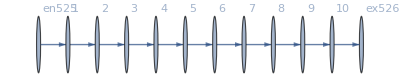

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j527→80.,j528→80.,j529→80.,j530→80.,j531→80.,j532→80.,j533→80.,j534→80.,j535→80.,j536→80.,j537→80.,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80.,jt551→80.,jt552→0.,jt553→80.,jt554→0.,jt555→80.,jt556→0.,jt557→80.,jt558→0.,jt559→80.,jt560→0.,jt561→80.,jt562→0.,jt563→80.,jt564→0.,jt565→80.,jt566→0.,jt567→80.,jt568→0.,u569→735.,u570→655.,u571→575.,u572→495.,u573→415.,u574→335.,u575→255.,u576→175.,u577→95.,u578→15.,u579→735.,u580→655.,u581→575.,u582→495.,u583→415.,u584→335.,u585→255.,u586→175.,u587→95.,u588→15.,u589→15.,u590→735.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→38.2376,u570→35.6556,u571→33.0737,u572→30.4917,u573→27.9098,u574→25.3278,u575→22.7459,u576→20.1639,u577→17.582,u578→15.,u579→38.2376,u580→35.6556,u581→33.0737,u582→30.4917,u583→27.9098,u584→25.3278,u585→22.7459,u586→20.1639,u587→17.582,u588→15.,u589→15.,u590→38.2376|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→43.4521,u570→40.2907,u571→37.1294,u572→33.968,u573→30.8067,u574→27.6454,u575→24.484,u576→21.3227,u577→18.1613,u578→15.,u579→43.4521,u580→40.2907,u581→37.1294,u582→33.968,u583→30.8067,u584→27.6454,u585→24.484,u586→21.3227,u587→18.1613,u588→15.,u589→15.,u590→43.4521|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→60.215,u570→55.1911,u571→50.1672,u572→45.1433,u573→40.1195,u574→35.0956,u575→30.0717,u576→25.0478,u577→20.0239,u578→15.,u579→60.215,u580→55.1911,u581→50.1672,u582→45.1433,u583→40.1195,u584→35.0956,u585→30.0717,u586→25.0478,u587→20.0239,u588→15.,u589→15.,u590→60.215|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.55795×10^-13,ComplexInfinity]

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→735.,u570→655.,u571→575.,u572→495.,u573→415.,u574→335.,u575→255.,u576→175.,u577→95.,u578→15.,u579→735.,u580→655.,u581→575.,u582→495.,u583→415.,u584→335.,u585→255.,u586→175.,u587→95.,u588→15.,u589→15.,u590→735.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.29622×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.29622×10^-16

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→3290.15,u570→2926.25,u571→2562.34,u572→2198.43,u573→1834.53,u574→1470.62,u575→1106.72,u576→742.811,u577→378.906,u578→15.,u579→3290.15,u580→2926.25,u581→2562.34,u582→2198.43,u583→1834.53,u584→1470.62,u585→1106.72,u586→742.811,u587→378.906,u588→15.,u589→15.,u590→3290.15|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→2.6104×10^6,u570→2.32036×10^6,u571→2.03032×10^6,u572→1.74027×10^6,u573→1.45023×10^6,u574→1.16019×10^6,u575→870144.,u576→580101.,u577→290058.,u578→15.,u579→2.6104×10^6,u580→2.32036×10^6,u581→2.03032×10^6,u582→1.74027×10^6,u583→1.45023×10^6,u584→1.16019×10^6,u585→870144.,u586→580101.,u587→290058.,u588→15.,u589→15.,u590→2.6104×10^6|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.28307×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.28307×10^-16

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→1.40355×10^8,u570→1.2476×10^8,u571→1.09165×10^8,u572→9.357×10^7,u573→7.7975×10^7,u574→6.238×10^7,u575→4.6785×10^7,u576→3.119×10^7,u577→1.5595×10^7,u578→15.,u579→1.40355×10^8,u580→1.2476×10^8,u581→1.09165×10^8,u582→9.357×10^7,u583→7.7975×10^7,u584→6.238×10^7,u585→4.6785×10^7,u586→3.119×10^7,u587→1.5595×10^7,u588→15.,u589→15.,u590→1.40355×10^8|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.9109×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.9109×10^-16

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→5.04333×10^19,u570→4.48296×10^19,u571→3.92259×10^19,u572→3.36222×10^19,u573→2.80185×10^19,u574→2.24148×10^19,u575→1.68111×10^19,u576→1.12074×10^19,u577→5.6037×10^18,u578→15.,u579→5.04333×10^19,u580→4.48296×10^19,u581→3.92259×10^19,u582→3.36222×10^19,u583→2.80185×10^19,u584→2.24148×10^19,u585→1.68111×10^19,u586→1.12074×10^19,u587→5.6037×10^18,u588→15.,u589→15.,u590→5.04333×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.07956×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.07956×10^-16

<|j527→80,j528→80,j529→80,j530→80,j531→80,j532→80,j533→80,j534→80,j535→80,j536→80,j537→80,j538→0.,j539→0.,j540→0.,j541→0.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,j548→0.,jt549→0.,jt550→80,jt551→80,jt552→0.,jt553→80,jt554→0.,jt555→80,jt556→0.,jt557→80,jt558→0.,jt559→80,jt560→0.,jt561→80,jt562→0.,jt563→80,jt564→0.,jt565→80,jt566→0.,jt567→80,jt568→0.,u569→1.98441×10^107,u570→1.76392×10^107,u571→1.54343×10^107,u572→1.32294×10^107,u573→1.10245×10^107,u574→8.81959×10^106,u575→6.61469×10^106,u576→4.4098×10^106,u577→2.2049×10^106,u578→15.,u579→1.98441×10^107,u580→1.76392×10^107,u581→1.54343×10^107,u582→1.32294×10^107,u583→1.10245×10^107,u584→8.81959×10^106,u585→6.61469×10^106,u586→4.4098×10^106,u587→2.2049×10^106,u588→15.,u589→15.,u590→1.98441×10^107|>